{20,10}

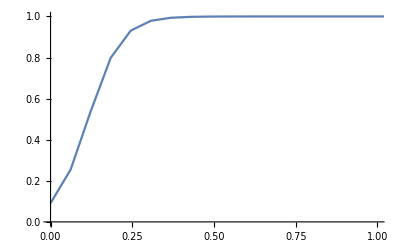

```mathematica
{sa,sb}={20,10}
Plot[ⅇ^(sa*s)/(sb+ⅇ^(sa*s)),{s,0,200},PlotRange->{{0,1},{0,1}}]
```

{0.25,100}

1

1

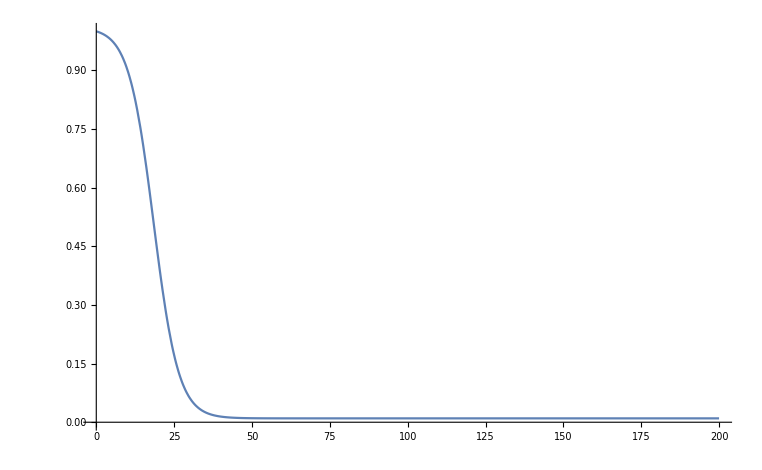

```mathematica
{sa,sb}={.25,100}
sz=1
w=1
Plot[(2+sb)/(1+sb)-ⅇ^(sa*s)/(sb+ⅇ^(sa*s)),{s,0,200},PlotRange->{0,1}]
```

```mathematica
pTatter[ttrA_,ttrB_,x_]:=(2+ttrB)/(1+ttrB)-ⅇ^(ttrA*x)/(ttrB+ⅇ^(ttrA*x))
Manipulate[
Plot[pTatter[a,b,x],{x,0,100},PlotRange->{0,1}]
,{a,0,1}
,{b,1,100}
]
```

```mathematica
pSenesce[ttrA_,ttrB_,x_]:=(2+ttrB)/(1+ttrB)-ⅇ^(ttrA*x)/(ttrB+ⅇ^(ttrA*x))
Manipulate[
Plot[pTatter[a,b,x],{x,0,100},PlotRange->{0,1}]
,{a,0,1}
,{b,1,100}
]
```